## Full Algorithm

{{{4.66194,4.55515},{8.86931,3.26527},{7.71686,9.66897},{1.99558,7.88657},{3.74724,7.67208},{9.68951,0.12693}},{{0.681721,7.52041},{1.26853,1.67192},{6.06263,9.88578},{7.0121,0.422725},{9.97502,5.49917}},{{0.301081,6.70885},{0.734242,2.39169},{3.4063,9.73921},{4.37961,0.0386382},{7.71161,9.20085},{8.49214,1.4216},{9.97502,5.49917}}}

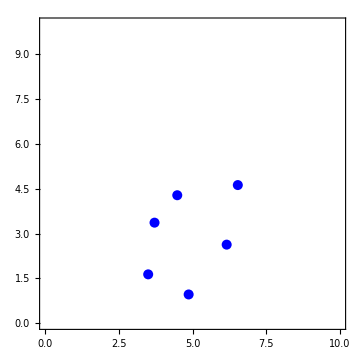

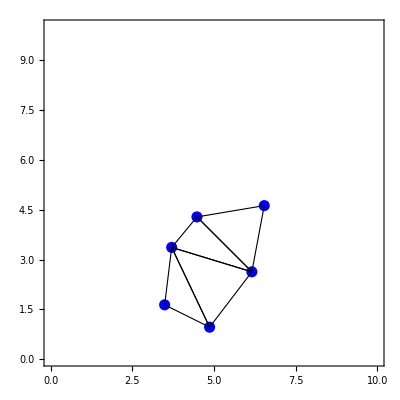
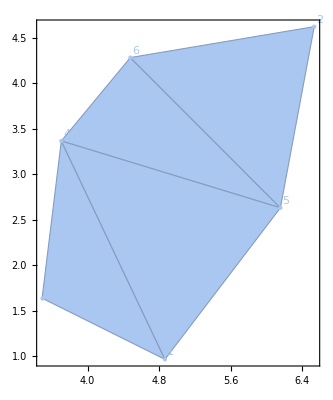

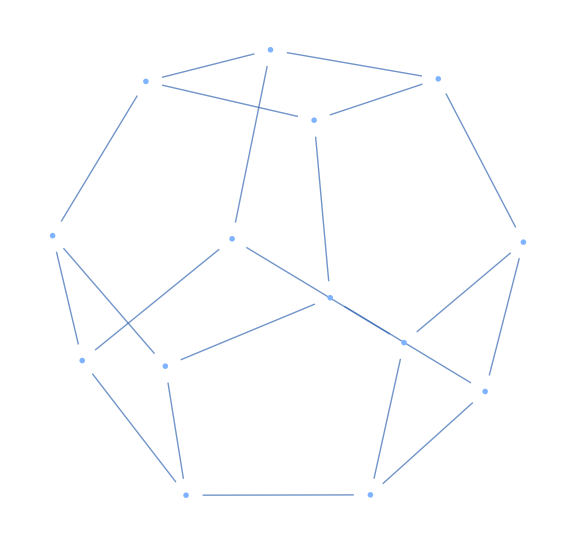

```mathematica
(* User parameters *)
numpoints=6;
bound=10;
randomizePoints=True;
repeatPoints=True;
showInitial=True;
showAllGraphics=True;

(* Notable point sets *)
notablePointSets={
{{4.661941227920847,4.555151780903351},{8.869314317650481,3.2652712296730257},{7.716860141665979,9.668974675183865},{1.9955821085368761,7.88656581949396},{3.747244613987405,7.67208271342605},{9.689510363097064,0.12692976388395572}},
(* Regular pentagon *)
PolygonCoordinates[RegularPolygon[{5,5},{5,0.1},5]],
(* Regular hexagon *)
PolygonCoordinates[RegularPolygon[{5,5},{5,0.1},7]]
}

If[randomizePoints,
(* Generate random set of points *)
If[repeatPoints,pts=RandomReal[bound,{numpoints,2}];],

(* Use user points *)
pts=PolygonCoordinates[RegularPolygon[{5,5},{5,0.1},7]];

];

(* Initial point set graphic *)
initialPointSet=Graphics[{Blue,PointSize[0.02],Point[pts]},Frame->True,PlotRange->{{0,bound},{0,bound}},ImageSize->Medium];

(* Load package *)
Needs["TriangleLink`"];
(* Construct delaunay triangulation *)
delTri=Sort[TriangleDelaunay[pts][[2]]];
(* Set up flip graph variables *)
triangulations={delTri};
sortedTriangulations={Sort[Sort/@delTri]};
edges={};

(* Save intermediary graphics *)
delTriGraphic=Graphics[{{Blue,PointSize[0.02],Point[pts]},{EdgeForm[Black],FaceForm[],GraphicsComplex[pts,Polygon[triangulations[[1]]]]}},Frame->True,PlotRange->{{0,bound},{0,bound}}];
delTriMesh=HighlightMesh[MeshRegion[pts,Polygon[triangulations[[1]]],Frame->True],Labeled[0,"Index"]];

(* Queue tracks triangulations that still need to be explored *)
(* Start with just the Delaunay triangulation *)
queue={1};

While[Length[queue]>0,
(* Pop the queue by removing and saving the first element *)
currIndex=First[queue];
currTriangulation=triangulations[[currIndex]];
queue=Rest[queue];

(* Find the convex quadrilaterals of the current triangulation *)

(* Loop through each triangle T1 except for the last *)
For[i=1,i<Length[currTriangulation],++i,
(* Loop through each triangle T2 that comes after T1 *)
For[j=i+1,j<=Length[currTriangulation],++j,
(* Get the union of the points that describe T1 and T2 *)
comb=Union@@currTriangulation[[{i,j}]];

(* If the union has 4 points, then T1 and T2 share an edge and their union forms a quadrilateral *)
If[Length[comb]==4,
(* Find the index of the point in the union that has the lowest y-value (right x-value in ties) - which becomes the anchor point *)
minIndex=Sort[MinimalBy[{1,2,3,4},pts[[comb[[#]],2]]&],#1[[1]]>#2[[1]]&][[1]];

(* Swap the first point and the anchor point *)
comb[[{1,minIndex}]]=comb[[{minIndex,1}]];
(* Sort the other three points by their angle to the anchor point from the right horizontal, in descending order *)
comb[[2;;]]=Sort[comb[[2;;]],PositivelyOrientedPoints[{pts[[#1]],pts[[comb[[1]]]],pts[[#2]]}]&];

(* Check if the quadrilateral is convex *)
If[ConvexRegionQ[MeshRegion[pts,Polygon[comb]]],
newTriangulation=currTriangulation;

(* Find the two shared points of the two triangles *)
shared=Intersection@@currTriangulation[[{i,j}]];
(* Find the two unshared points of the two triangles *)
unshared=SymmetricDifference@@currTriangulation[[{i,j}]];

(* Create a new triangle consisting of the unshared points plus one of the shared *)
newT1=Append[unshared,shared[[1]]];
(* Rearrange the order of the points so that the triangle is described in counter clockwise order *)
If[PositivelyOrientedPoints[newT1],newT1=Reverse[newT1]];

(* Repeat for the other shared point *)
newT2=Append[unshared,shared[[2]]];
If[PositivelyOrientedPoints[newT2],newT2=Reverse[newT2]];

(* Replace the triangles of the convex quadrilateral with the new triangles to reflect the edge flip *)
newTriangulation[[{i,j}]]={newT1,newT2};
sortedNewTriangulation=Sort[Sort/@newTriangulation];

(* Verify if the new triangulation is new globally *)
If[!MemberQ[sortedTriangulations,sortedNewTriangulation],
(* Triangulation is new, add it *)
triangulations=Append[triangulations,newTriangulation];
sortedTriangulations=Append[sortedTriangulations,sortedNewTriangulation];

(* Record connection between the current and the new triangulation *)
newIndex=Length[triangulations];
edges=Append[edges,{currIndex,newIndex}];

(* Push index of new triangulation to the queue *)
queue=Append[queue,newIndex],

(* Trianglation is not new, check for edge and add it if not yet included *)
newIndex=Position[sortedTriangulations,sortedNewTriangulation][[1,1]];
newEdge=Sort[{currIndex,newIndex}];
If[!MemberQ[edges,newEdge],edges=Append[edges,newEdge]]
];
];
];
];
];
];

(* Generate mesh regions from each triangulation of the flip graph to use as vertices *)
vertexShapes={};
For[i=1,i<=Length[triangulations],++i,
vertexShapes=Append[vertexShapes,i->MeshRegion[pts,Polygon[triangulations[[i]]]]];
];

(* Display extra graphics if desired *)
If[showInitial,Print[initialPointSet]];
If[showAllGraphics,Print[delTriGraphic,delTriMesh]];

(* Display the flip graph *)
Graph[edges,VertexShape->vertexShapes,VertexSize->Large,ImageSize->Large]
```